/net/people/faculty/physics/awhitten/aod-research/bajennissen/day207/aod

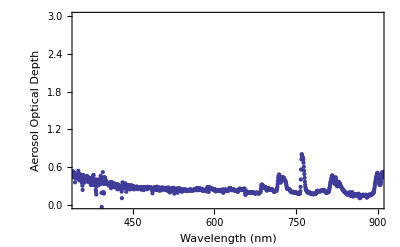

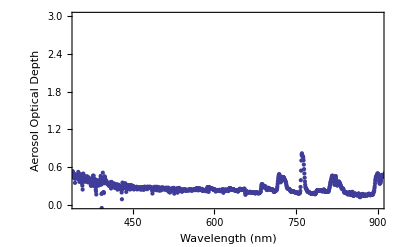

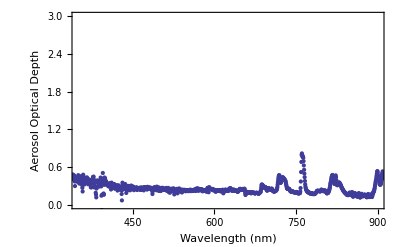

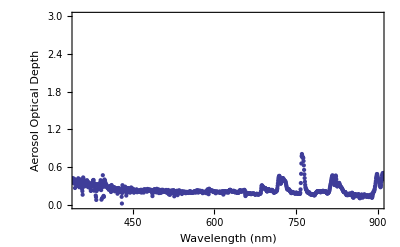

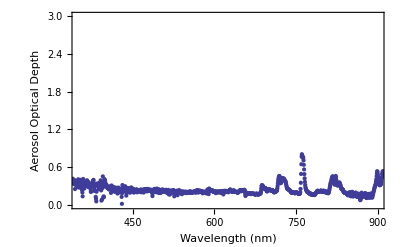

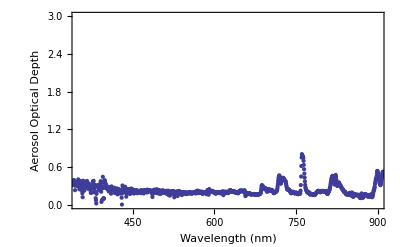

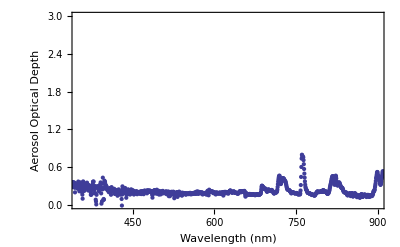

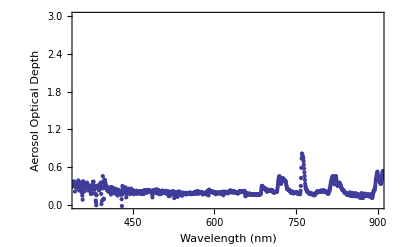

```mathematica
SetDirectory["/usr/people/faculty/physics/awhitten/aod-research/bajennissen/day207/aod"]
Clear[farray];
farray=FileNames["*.aod"];
size=FileNames["*.aod"]//Length;
For[i=1,i<size+1,i++,data=Import[farray[[i]]];x=ListPlot[data,PlotRange->{{350,900},{0,3}},Frame->True, FrameLabel->{"Wavelength (nm)", "Aerosol Optical Depth",farray[[i]],""}];Print[x]]
Manipulate[ListPlot[Import[farray[[i]]],PlotRange->{{350,900},{0,3}},Frame->True, FrameLabel->{"Wavelength (nm)", "Aerosol Optical Depth",farray[[i]],""}],{i,1,size,1}]
```